# 7 Feb 2017 NW GaAs mesa 1200/100

```mathematica
ClearAll[feb7]
feb7=Table[Import["C:\\Users\\tonie\\Desktop\\учеба\\НИР\\Data\\2017\\feb\\7\\7feb_acuun_"<>ToString[i]<>".dat"],{i,1,11}];
```

```mathematica
ClearAll[allDat,short1200100, long1200100]
short1200100 = {"short1200100",feb7[[{2,3,6,7,10}]]};
long1200100 = {"long1200100",feb7[[{1,4,5,8,9}]]};
long1200100[[2,1,All,3]] = long1200100[[2,1,All,3]]+11.218226941176406;
long1200100[[2,2,All,3]] = long1200100[[2,2,All,3]]+11.218226941176406;
allDat={short1200100, long1200100};
```

```mathematica
ClearAll[powerDatDict]
powerDatDict = 
<|
"short1200100"->{0.5,1,1.5,2,3},
"long1200100"->{0.5,1,1.5,2,3}
|>;
```

```mathematica
TableForm[Table[Table[allDat[[j]][[2,i]][[1,1]],{i,Length[allDat[[j,2]]]}],{j,Length[allDat]}]]
```

-101. | -101. | -101. | -101. | -101.
-101. | -101. | -98.9002 | -98.9001 | -98.9001

#### All measures

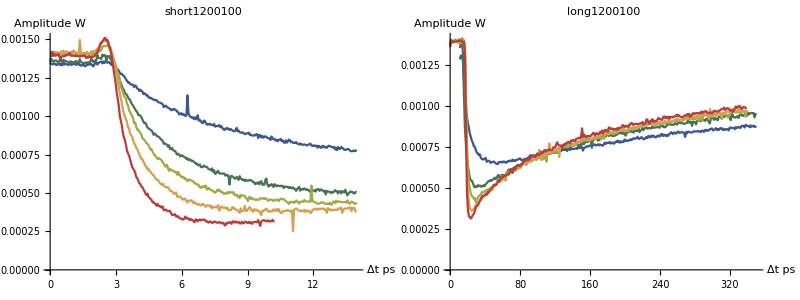

```mathematica
TableForm[
Partition[
Table[
ListLinePlot[
Table[dat[[2,i]][[All,{3,2}]],{i,1,Length[dat[[2]]]}],
ImageSize->450,
AxesLabel->{"Δt ps","Amplitude W"},
PlotLabel->dat[[1]],
LabelStyle->15,
PlotStyle->"DarkRainbow",
PlotRange->All],
{dat,allDat}],
2]
]
```

#### Normalization

```mathematica
amplitudes=
Table[
{
dat[[1]],
Table[
MeanFilter[
(dat[[2]][[i,All,2]]+(Max[dat[[2]][[All,1,2]]]-dat[[2]][[i,1,2]]))/Max[dat[[2]][[All,1,2]]],
1],
{i,1,Length[dat[[2]]]}]
},
{dat,{short1200100, long1200100}}];
```

```mathematica
normDatDic = 
Association[
Table[
amplitudes[[i,1]]->
Table[
Transpose[{allDat[[i,2]][[j,All,3]],amplitudes[[i,2]][[j]]}],
{j,Length[allDat[[i,2]]]}],
{i,Length[amplitudes]}
]
];
```

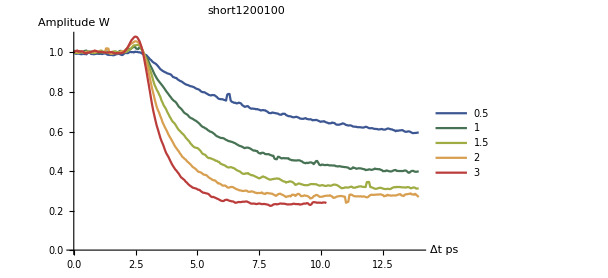
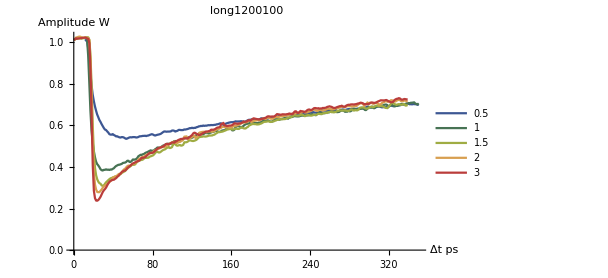
-Graphics- | -Graphics-

```mathematica
TableForm[
Partition[
Table[
ListLinePlot[
normDatDic[name],
ImageSize->450,
AxesLabel->{"Δt ps","Amplitude W"},
PlotLabel->name,
LabelStyle->15,
PlotStyle->"DarkRainbow",
PlotRange->All,
PlotLegends->powerDatDict[name]],
{name,{"short1200100","long1200100"}}],
2]
]
```

#### Logarithmic scaling

```mathematica
normLogDatDic = 
Association[
Table[
amplitudes[[i,1]]->
Table[
Transpose[{allDat[[i,2]][[j,All,3]],Log[amplitudes[[i,2]][[j]]]}],
{j,Length[allDat[[i,2]]]}],
{i,Length[amplitudes]}
]
];
```

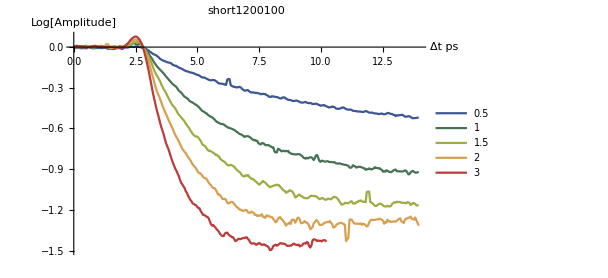
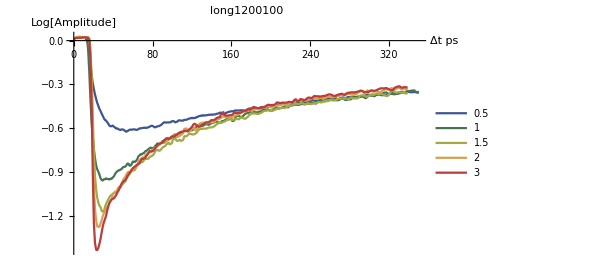
-Graphics- | -Graphics-

```mathematica
TableForm[
Partition[
Table[
ListLinePlot[
normLogDatDic[name],
ImageSize->450,
AxesLabel->{"Δt ps","Log[Amplitude]"},
PlotLabel->name,
LabelStyle->15,
PlotStyle->"DarkRainbow",
PlotRange->All,
PlotLegends->powerDatDict[name]],
{name,{"short1200100","long1200100"}}],
2]
]
```

#### Short dynamic for mesa 1200/100

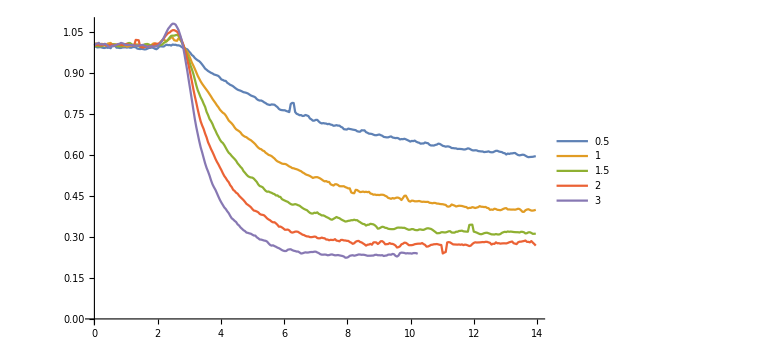

```mathematica
ListLinePlot[normDatDic["short1200100"],PlotLegends->powerDatDict["short1200100"],ImageSize->Large]
```

Linear area for this mesa

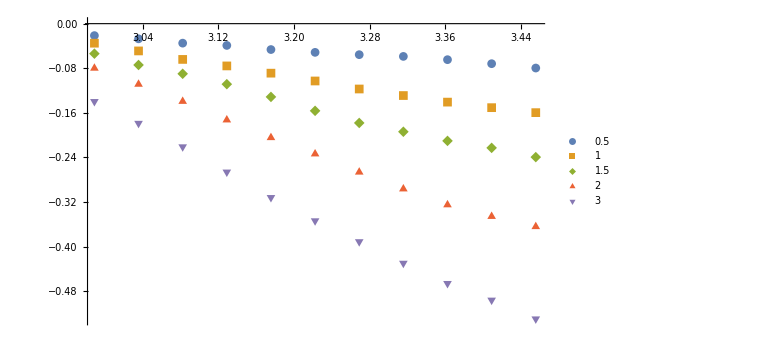

```mathematica
ListPlot[normLogDatDic["short1200100"][[All,65;;75]],PlotLegends->powerDatDict["short1200100"],ImageSize->Large,PlotMarkers->Automatic]
```

```mathematica
lineEreaShort1200100 = normLogDatDic["short1200100"][[All,65;;75]];
```

```mathematica
lineCoefShort1200100 = Table[FindFit[lineEreaShort1200100[[i]],a t+b,{a,b},t],{i,1,Length[lineEreaShort1200100]}];
```

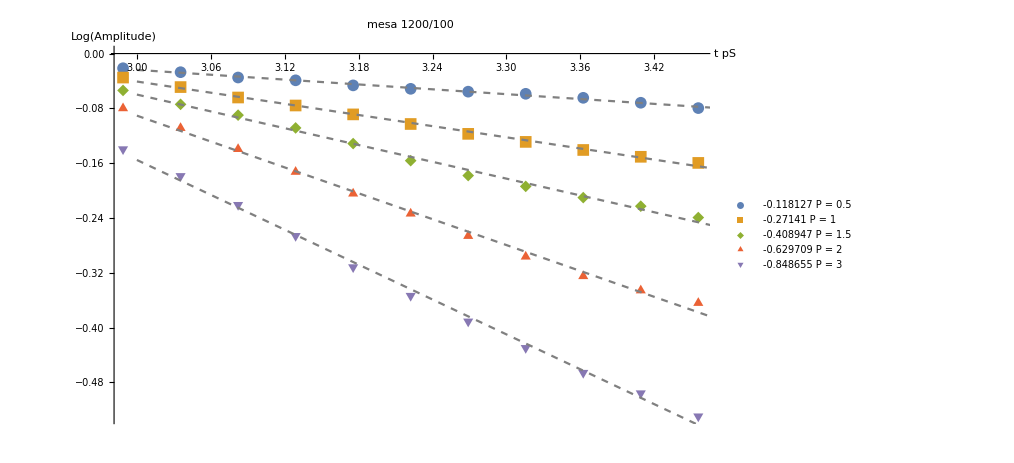

```mathematica
Show[
ListPlot[
Table[lineEreaShort1200100[[i]],{i,1,5}],
PlotLegends->Table[ToString[lineCoefShort1200100[[i,1,2]]]<>"    P = "<>ToString[powerDatDict["short1200100"][[i]]],{i,1,5}],
ImageSize->750,
PlotLabel->"mesa 1200/100",
AxesLabel->{"t pS","Log(Amplitude)"},
LabelStyle->18,
PlotMarkers->{Automatic,12}
],
Plot[
Table[a x+b/.lineCoefShort1200100[[i]],{i,1,5}],
{x,3,3.5},
PlotStyle->{Gray,Dashed}
]
]
```

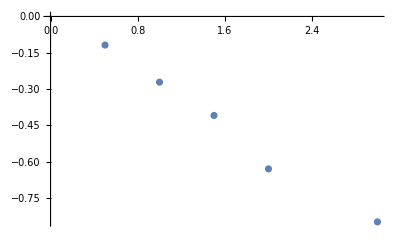

```mathematica
ListPlot[Sort[Table[{powerDatDict["short1200100"][[i]],lineCoefShort1200100[[i,1,2]]},{i,1,5}]]]
```